```mathematica
data0=Import["data0.txt","Data"];
```

```mathematica
x0=Mean[Transpose[data0][[1]]]//N
```

440.845

```mathematica
y0=Mean[Transpose[data0][[2]]]//N
```

422.586

```mathematica
z0=Mean[Transpose[data0][[3]]]//N
```

537.975

```mathematica
data1=Import["data1.txt","Data"];
```

```mathematica
x1=Mean[Transpose[data1][[1]]]//N
```

415.911

```mathematica
y1=Mean[Transpose[data1][[2]]]//N
```

396.779

```mathematica
z1=Mean[Transpose[data1][[3]]]//N
```

516.838

```mathematica
data2=Import["data2.txt","Data"];
```

```mathematica
x0=Mean[Transpose[data2][[1]]]//N
```

402.387

```mathematica
y0=Mean[Transpose[data2][[2]]]//N
```

385.125

```mathematica
z0=Mean[Transpose[data2][[3]]]//N
```

504.732

```mathematica
Length[data2]
```

76643

```mathematica
data3=Import["data3.txt","Data"];
```

```mathematica
x0=Mean[Transpose[data3][[1]]]//N
```

400.433

```mathematica
y0=Mean[Transpose[data3][[2]]]//N
```

383.304

```mathematica
z0=Mean[Transpose[data3][[3]]]//N
```

502.788

```mathematica
Length[data3]
```

77217

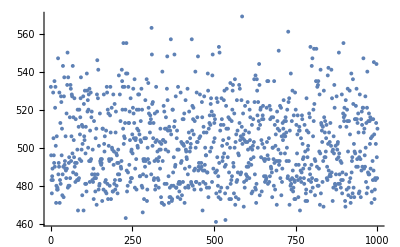

```mathematica
ListPlot[Transpose[data3][[3]][[1;;1000]]]
```

```mathematica
σx=√Sum[(Transpose[data3][[1,i]]-x0)^2/Length[data3],{i,1,Length[data3]}]
```

20.2827

```mathematica
data4=Import["data4.txt","Data"];
```

```mathematica
x0=Mean[Transpose[data4][[1]]]//N
```

403.285

```mathematica
y0=Mean[Transpose[data4][[2]]]//N
```

385.874

```mathematica
z0=Mean[Transpose[data4][[3]]]//N
```

505.442

```mathematica
Length[data4]
```

340225

```mathematica
σx=√Sum[(Transpose[data4][[1,i]]-x0)^2/Length[data4],{i,1,Length[data4]}]
```

19.192